```mathematica
ClearAll
```

ClearAll

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.694285},{0.02,0.688541},{0.03,0.682768},{0.04,0.676965},{0.05,0.671134},{0.06,0.665275},{0.07,0.659387},{0.08,0.653471},{0.09,0.647526},{0.1,0.641554},{0.11,0.635554},{0.12,0.629526},{0.13,0.62347},{0.14,0.617388},{0.15,0.611278},{0.16,0.605141},{0.17,0.598978},{0.18,0.592788},{0.19,0.586572},{0.2,0.580329},{0.21,0.574061},{0.22,0.567768},{0.23,0.561449},{0.24,0.555104},{0.25,0.548736},{0.26,0.542342},{0.27,0.535925},{0.28,0.529484},{0.29,0.52302},{0.3,0.516532},{0.31,0.510022},{0.32,0.50349},{0.33,0.496937},{0.34,0.490362},{0.35,0.483766},{0.36,0.477151},{0.37,0.470516},{0.38,0.463862},{0.39,0.45719},{0.4,0.4505},{0.41,0.443794},{0.42,0.437071},{0.43,0.430333},{0.44,0.42358},{0.45,0.416814},{0.46,0.410035},{0.47,0.403244},{0.48,0.396441},{0.49,0.389629},{0.5,0.382809},{0.51,0.37598},{0.52,0.369144},{0.53,0.362304},{0.54,0.355458},{0.55,0.34861},{0.56,0.341761},{0.57,0.334911},{0.58,0.328062},{0.59,0.321215},{0.6,0.314373},{0.61,0.307537},{0.62,0.300708},{0.63,0.293888},{0.64,0.287079},{0.65,0.280282},{0.66,0.2735},{0.67,0.266735},{0.68,0.259988},{0.69,0.253261},{0.7,0.246557},{0.71,0.239877},{0.72,0.233224},{0.73,0.226601},{0.74,0.220009},{0.75,0.213451},{0.76,0.206929},{0.77,0.200447},{0.78,0.194005},{0.79,0.187608},{0.8,0.181258},{0.81,0.174958},{0.82,0.16871},{0.83,0.162517},{0.84,0.156382},{0.85,0.150309},{0.86,0.144301},{0.87,0.138359},{0.88,0.132489},{0.89,0.126692},{0.9,0.120973},{0.91,0.115335},{0.92,0.10978},{0.93,0.104313},{0.94,0.098937},{0.95,0.0936555},{0.96,0.0884724},{0.97,0.0833911},{0.98,0.0784155},{0.99,0.0735493},{1.,0.0687964}}

{{0.,0.3},{0.01,0.305715},{0.02,0.311459},{0.03,0.317232},{0.04,0.323035},{0.05,0.328866},{0.06,0.334725},{0.07,0.340613},{0.08,0.346529},{0.09,0.352474},{0.1,0.358446},{0.11,0.364446},{0.12,0.370474},{0.13,0.37653},{0.14,0.382612},{0.15,0.388722},{0.16,0.394859},{0.17,0.401022},{0.18,0.407212},{0.19,0.413428},{0.2,0.419671},{0.21,0.425939},{0.22,0.432232},{0.23,0.438551},{0.24,0.444896},{0.25,0.451264},{0.26,0.457658},{0.27,0.464075},{0.28,0.470516},{0.29,0.47698},{0.3,0.483468},{0.31,0.489978},{0.32,0.49651},{0.33,0.503063},{0.34,0.509638},{0.35,0.516234},{0.36,0.522849},{0.37,0.529484},{0.38,0.536138},{0.39,0.54281},{0.4,0.5495},{0.41,0.556206},{0.42,0.562929},{0.43,0.569667},{0.44,0.57642},{0.45,0.583186},{0.46,0.589965},{0.47,0.596756},{0.48,0.603559},{0.49,0.610371},{0.5,0.617191},{0.51,0.62402},{0.52,0.630856},{0.53,0.637696},{0.54,0.644542},{0.55,0.65139},{0.56,0.658239},{0.57,0.665089},{0.58,0.671938},{0.59,0.678785},{0.6,0.685627},{0.61,0.692463},{0.62,0.699292},{0.63,0.706112},{0.64,0.712921},{0.65,0.719718},{0.66,0.7265},{0.67,0.733265},{0.68,0.740012},{0.69,0.746739},{0.7,0.753443},{0.71,0.760123},{0.72,0.766776},{0.73,0.773399},{0.74,0.779991},{0.75,0.786549},{0.76,0.793071},{0.77,0.799553},{0.78,0.805995},{0.79,0.812392},{0.8,0.818742},{0.81,0.825042},{0.82,0.83129},{0.83,0.837483},{0.84,0.843618},{0.85,0.849691},{0.86,0.855699},{0.87,0.861641},{0.88,0.867511},{0.89,0.873308},{0.9,0.879027},{0.91,0.884665},{0.92,0.89022},{0.93,0.895687},{0.94,0.901063},{0.95,0.906344},{0.96,0.911528},{0.97,0.916609},{0.98,0.921584},{0.99,0.926451},{1.,0.931204}}

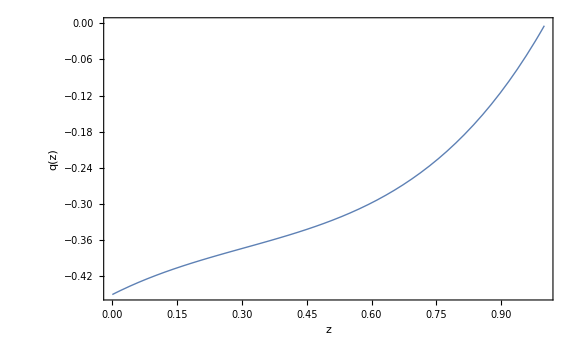

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.692853},{0.02,0.685702},{0.03,0.678551},{0.04,0.671402},{0.05,0.664257},{0.06,0.657119},{0.07,0.64999},{0.08,0.642871},{0.09,0.635766},{0.1,0.628675},{0.11,0.621601},{0.12,0.614546},{0.13,0.607511},{0.14,0.600498},{0.15,0.593509},{0.16,0.586545},{0.17,0.579608},{0.18,0.572698},{0.19,0.565818},{0.2,0.558969},{0.21,0.552151},{0.22,0.545367},{0.23,0.538617},{0.24,0.531902},{0.25,0.525223},{0.26,0.518581},{0.27,0.511978},{0.28,0.505413},{0.29,0.498889},{0.3,0.492405},{0.31,0.485962},{0.32,0.479562},{0.33,0.473204},{0.34,0.46689},{0.35,0.460619},{0.36,0.454394},{0.37,0.448213},{0.38,0.442078},{0.39,0.435988},{0.4,0.429946},{0.41,0.42395},{0.42,0.418001},{0.43,0.4121},{0.44,0.406247},{0.45,0.400442},{0.46,0.394686},{0.47,0.388978},{0.48,0.383319},{0.49,0.377709},{0.5,0.372149},{0.51,0.366639},{0.52,0.361178},{0.53,0.355766},{0.54,0.350405},{0.55,0.345094},{0.56,0.339833},{0.57,0.334621},{0.58,0.329461},{0.59,0.32435},{0.6,0.319289},{0.61,0.314279},{0.62,0.309319},{0.63,0.304409},{0.64,0.29955},{0.65,0.29474},{0.66,0.289981},{0.67,0.285271},{0.68,0.280611},{0.69,0.276001},{0.7,0.271441},{0.71,0.266931},{0.72,0.262469},{0.73,0.258057},{0.74,0.253695},{0.75,0.249381},{0.76,0.245116},{0.77,0.2409},{0.78,0.236732},{0.79,0.232613},{0.8,0.228542},{0.81,0.224518},{0.82,0.220543},{0.83,0.216615},{0.84,0.212734},{0.85,0.208901},{0.86,0.205114},{0.87,0.201374},{0.88,0.197681},{0.89,0.194033},{0.9,0.190432},{0.91,0.186876},{0.92,0.183366},{0.93,0.179901},{0.94,0.17648},{0.95,0.173105},{0.96,0.169773},{0.97,0.166486},{0.98,0.163243},{0.99,0.160043},{1.,0.156887}}

{{0.,0.3},{0.01,0.307147},{0.02,0.314298},{0.03,0.321449},{0.04,0.328598},{0.05,0.335743},{0.06,0.342881},{0.07,0.35001},{0.08,0.357129},{0.09,0.364234},{0.1,0.371325},{0.11,0.378399},{0.12,0.385454},{0.13,0.392489},{0.14,0.399502},{0.15,0.406491},{0.16,0.413455},{0.17,0.420392},{0.18,0.427302},{0.19,0.434182},{0.2,0.441031},{0.21,0.447849},{0.22,0.454633},{0.23,0.461383},{0.24,0.468098},{0.25,0.474777},{0.26,0.481419},{0.27,0.488022},{0.28,0.494587},{0.29,0.501111},{0.3,0.507595},{0.31,0.514038},{0.32,0.520438},{0.33,0.526796},{0.34,0.53311},{0.35,0.539381},{0.36,0.545606},{0.37,0.551787},{0.38,0.557922},{0.39,0.564012},{0.4,0.570054},{0.41,0.57605},{0.42,0.581999},{0.43,0.5879},{0.44,0.593753},{0.45,0.599558},{0.46,0.605314},{0.47,0.611022},{0.48,0.616681},{0.49,0.622291},{0.5,0.627851},{0.51,0.633361},{0.52,0.638822},{0.53,0.644234},{0.54,0.649595},{0.55,0.654906},{0.56,0.660167},{0.57,0.665379},{0.58,0.670539},{0.59,0.67565},{0.6,0.680711},{0.61,0.685721},{0.62,0.690681},{0.63,0.695591},{0.64,0.70045},{0.65,0.70526},{0.66,0.710019},{0.67,0.714729},{0.68,0.719389},{0.69,0.723999},{0.7,0.728559},{0.71,0.733069},{0.72,0.737531},{0.73,0.741943},{0.74,0.746305},{0.75,0.750619},{0.76,0.754884},{0.77,0.7591},{0.78,0.763268},{0.79,0.767387},{0.8,0.771458},{0.81,0.775482},{0.82,0.779457},{0.83,0.783385},{0.84,0.787266},{0.85,0.791099},{0.86,0.794886},{0.87,0.798626},{0.88,0.802319},{0.89,0.805967},{0.9,0.809568},{0.91,0.813124},{0.92,0.816634},{0.93,0.820099},{0.94,0.82352},{0.95,0.826895},{0.96,0.830227},{0.97,0.833514},{0.98,0.836757},{0.99,0.839957},{1.,0.843113}}

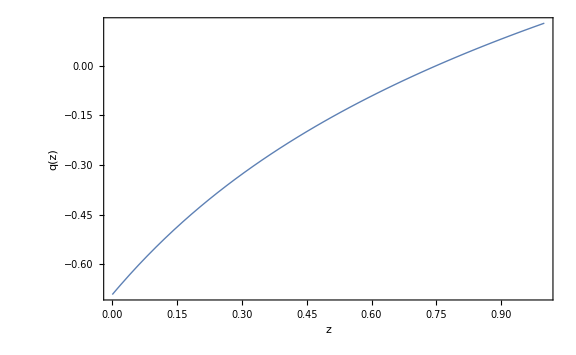

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.690002},{0.02,0.680083},{0.03,0.670251},{0.04,0.660516},{0.05,0.650883},{0.06,0.64136},{0.07,0.631952},{0.08,0.622664},{0.09,0.613501},{0.1,0.604466},{0.11,0.595562},{0.12,0.586792},{0.13,0.578158},{0.14,0.569662},{0.15,0.561306},{0.16,0.553089},{0.17,0.545013},{0.18,0.537078},{0.19,0.529283},{0.2,0.521629},{0.21,0.514115},{0.22,0.50674},{0.23,0.499503},{0.24,0.492402},{0.25,0.485438},{0.26,0.478607},{0.27,0.471909},{0.28,0.465341},{0.29,0.458903},{0.3,0.452592},{0.31,0.446406},{0.32,0.440344},{0.33,0.434402},{0.34,0.42858},{0.35,0.422875},{0.36,0.417285},{0.37,0.411808},{0.38,0.406442},{0.39,0.401185},{0.4,0.396033},{0.41,0.390987},{0.42,0.386042},{0.43,0.381198},{0.44,0.376452},{0.45,0.371802},{0.46,0.367246},{0.47,0.362782},{0.48,0.358408},{0.49,0.354122},{0.5,0.349922},{0.51,0.345806},{0.52,0.341773},{0.53,0.33782},{0.54,0.333946},{0.55,0.330149},{0.56,0.326428},{0.57,0.322779},{0.58,0.319203},{0.59,0.315697},{0.6,0.31226},{0.61,0.308889},{0.62,0.305585},{0.63,0.302344},{0.64,0.299166},{0.65,0.296049},{0.66,0.292992},{0.67,0.289993},{0.68,0.287052},{0.69,0.284166},{0.7,0.281335},{0.71,0.278557},{0.72,0.275832},{0.73,0.273157},{0.74,0.270532},{0.75,0.267956},{0.76,0.265427},{0.77,0.262944},{0.78,0.260507},{0.79,0.258115},{0.8,0.255766},{0.81,0.253459},{0.82,0.251194},{0.83,0.24897},{0.84,0.246785},{0.85,0.244639},{0.86,0.242531},{0.87,0.24046},{0.88,0.238425},{0.89,0.236426},{0.9,0.234462},{0.91,0.232531},{0.92,0.230634},{0.93,0.22877},{0.94,0.226937},{0.95,0.225136},{0.96,0.223365},{0.97,0.221624},{0.98,0.219912},{0.99,0.218228},{1.,0.216573}}

{{0.,0.3},{0.01,0.309998},{0.02,0.319917},{0.03,0.329749},{0.04,0.339484},{0.05,0.349117},{0.06,0.35864},{0.07,0.368048},{0.08,0.377336},{0.09,0.386499},{0.1,0.395534},{0.11,0.404438},{0.12,0.413208},{0.13,0.421842},{0.14,0.430338},{0.15,0.438694},{0.16,0.446911},{0.17,0.454987},{0.18,0.462922},{0.19,0.470717},{0.2,0.478371},{0.21,0.485885},{0.22,0.49326},{0.23,0.500497},{0.24,0.507598},{0.25,0.514562},{0.26,0.521393},{0.27,0.528091},{0.28,0.534659},{0.29,0.541097},{0.3,0.547408},{0.31,0.553594},{0.32,0.559656},{0.33,0.565598},{0.34,0.57142},{0.35,0.577125},{0.36,0.582715},{0.37,0.588192},{0.38,0.593558},{0.39,0.598815},{0.4,0.603967},{0.41,0.609013},{0.42,0.613958},{0.43,0.618802},{0.44,0.623548},{0.45,0.628198},{0.46,0.632754},{0.47,0.637218},{0.48,0.641592},{0.49,0.645878},{0.5,0.650078},{0.51,0.654194},{0.52,0.658227},{0.53,0.66218},{0.54,0.666054},{0.55,0.669851},{0.56,0.673572},{0.57,0.677221},{0.58,0.680797},{0.59,0.684303},{0.6,0.68774},{0.61,0.691111},{0.62,0.694415},{0.63,0.697656},{0.64,0.700834},{0.65,0.703951},{0.66,0.707008},{0.67,0.710007},{0.68,0.712948},{0.69,0.715834},{0.7,0.718665},{0.71,0.721443},{0.72,0.724168},{0.73,0.726843},{0.74,0.729468},{0.75,0.732044},{0.76,0.734573},{0.77,0.737056},{0.78,0.739493},{0.79,0.741885},{0.8,0.744234},{0.81,0.746541},{0.82,0.748806},{0.83,0.75103},{0.84,0.753215},{0.85,0.755361},{0.86,0.757469},{0.87,0.75954},{0.88,0.761575},{0.89,0.763574},{0.9,0.765538},{0.91,0.767469},{0.92,0.769366},{0.93,0.77123},{0.94,0.773063},{0.95,0.774864},{0.96,0.776635},{0.97,0.778376},{0.98,0.780088},{0.99,0.781772},{1.,0.783427}}

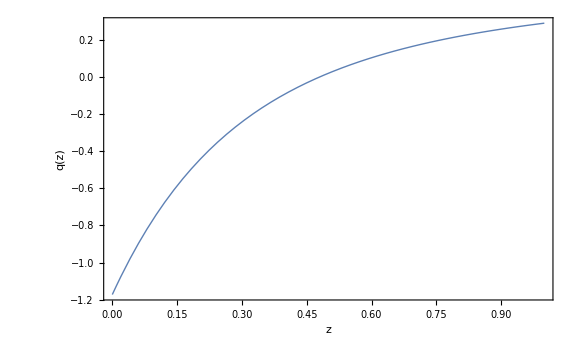

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,omegade[z]},{z,0,1,0.01}]
points8=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.688584},{0.02,0.677302},{0.03,0.666167},{0.04,0.655191},{0.05,0.644381},{0.06,0.633747},{0.07,0.623295},{0.08,0.61303},{0.09,0.602956},{0.1,0.593078},{0.11,0.583396},{0.12,0.573912},{0.13,0.564629},{0.14,0.555544},{0.15,0.546659},{0.16,0.537972},{0.17,0.529481},{0.18,0.521186},{0.19,0.513082},{0.2,0.505169},{0.21,0.497444},{0.22,0.489902},{0.23,0.482542},{0.24,0.47536},{0.25,0.468353},{0.26,0.461516},{0.27,0.454847},{0.28,0.448342},{0.29,0.441997},{0.3,0.435808},{0.31,0.429772},{0.32,0.423885},{0.33,0.418143},{0.34,0.412544},{0.35,0.407082},{0.36,0.401755},{0.37,0.39656},{0.38,0.391492},{0.39,0.386548},{0.4,0.381726},{0.41,0.377021},{0.42,0.372431},{0.43,0.367953},{0.44,0.363582},{0.45,0.359318},{0.46,0.355156},{0.47,0.351094},{0.48,0.347129},{0.49,0.343258},{0.5,0.339479},{0.51,0.335789},{0.52,0.332186},{0.53,0.328668},{0.54,0.325231},{0.55,0.321874},{0.56,0.318595},{0.57,0.315392},{0.58,0.312262},{0.59,0.309203},{0.6,0.306213},{0.61,0.303292},{0.62,0.300435},{0.63,0.297643},{0.64,0.294913},{0.65,0.292244},{0.66,0.289633},{0.67,0.28708},{0.68,0.284583},{0.69,0.28214},{0.7,0.27975},{0.71,0.277411},{0.72,0.275123},{0.73,0.272883},{0.74,0.270691},{0.75,0.268545},{0.76,0.266445},{0.77,0.264388},{0.78,0.262374},{0.79,0.260402},{0.8,0.25847},{0.81,0.256579},{0.82,0.254726},{0.83,0.25291},{0.84,0.251132},{0.85,0.249389},{0.86,0.247681},{0.87,0.246007},{0.88,0.244367},{0.89,0.242759},{0.9,0.241183},{0.91,0.239637},{0.92,0.238122},{0.93,0.236636},{0.94,0.23518},{0.95,0.233751},{0.96,0.232349},{0.97,0.230974},{0.98,0.229626},{0.99,0.228303},{1.,0.227005}}

{{0.,0.3},{0.01,0.311416},{0.02,0.322698},{0.03,0.333833},{0.04,0.344809},{0.05,0.355619},{0.06,0.366253},{0.07,0.376705},{0.08,0.38697},{0.09,0.397044},{0.1,0.406922},{0.11,0.416604},{0.12,0.426088},{0.13,0.435371},{0.14,0.444456},{0.15,0.453341},{0.16,0.462028},{0.17,0.470519},{0.18,0.478814},{0.19,0.486918},{0.2,0.494831},{0.21,0.502556},{0.22,0.510098},{0.23,0.517458},{0.24,0.52464},{0.25,0.531647},{0.26,0.538484},{0.27,0.545153},{0.28,0.551658},{0.29,0.558003},{0.3,0.564192},{0.31,0.570228},{0.32,0.576115},{0.33,0.581857},{0.34,0.587456},{0.35,0.592918},{0.36,0.598245},{0.37,0.60344},{0.38,0.608508},{0.39,0.613452},{0.4,0.618274},{0.41,0.622979},{0.42,0.627569},{0.43,0.632047},{0.44,0.636418},{0.45,0.640682},{0.46,0.644844},{0.47,0.648906},{0.48,0.652871},{0.49,0.656742},{0.5,0.660521},{0.51,0.664211},{0.52,0.667814},{0.53,0.671332},{0.54,0.674769},{0.55,0.678126},{0.56,0.681405},{0.57,0.684608},{0.58,0.687738},{0.59,0.690797},{0.6,0.693787},{0.61,0.696708},{0.62,0.699565},{0.63,0.702357},{0.64,0.705087},{0.65,0.707756},{0.66,0.710367},{0.67,0.71292},{0.68,0.715417},{0.69,0.71786},{0.7,0.72025},{0.71,0.722589},{0.72,0.724877},{0.73,0.727117},{0.74,0.729309},{0.75,0.731455},{0.76,0.733555},{0.77,0.735612},{0.78,0.737626},{0.79,0.739598},{0.8,0.74153},{0.81,0.743421},{0.82,0.745274},{0.83,0.74709},{0.84,0.748868},{0.85,0.750611},{0.86,0.752319},{0.87,0.753993},{0.88,0.755633},{0.89,0.757241},{0.9,0.758817},{0.91,0.760363},{0.92,0.761878},{0.93,0.763364},{0.94,0.76482},{0.95,0.766249},{0.96,0.767651},{0.97,0.769026},{0.98,0.770374},{0.99,0.771697},{1.,0.772995}}

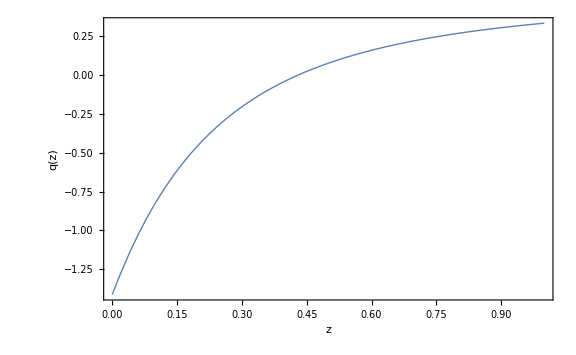

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

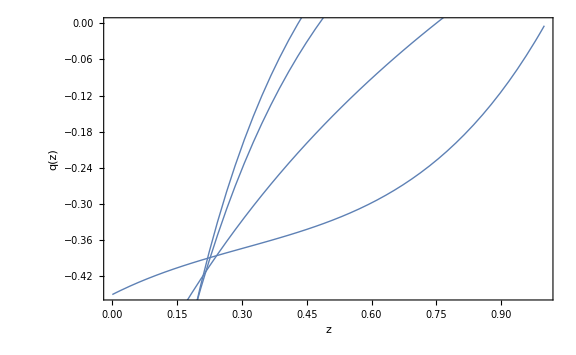

```mathematica
Show[p04n, p02n, p02, p04]
```

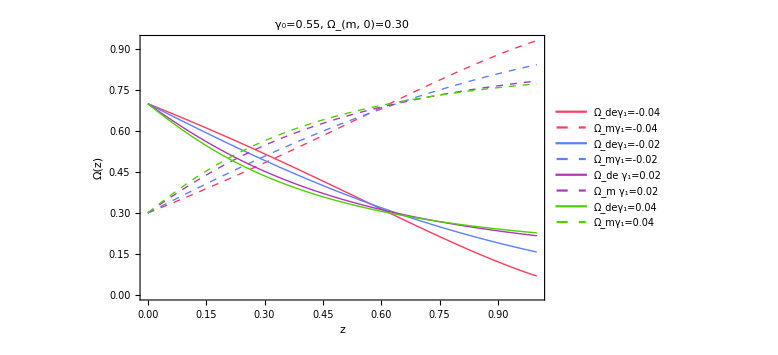

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7, points4, points8}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_1=-0.04","Ω_mγ_1=-0.04", "Ω_deγ_1=-0.02","Ω_mγ_1=-0.02", "Ω_de γ_1=0.02", "Ω_m γ_1=0.02","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.30", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
Export["omega(z)_gamma1_om0.30.pdf",list2,ImageResolution->500]
```

omega(z)_gamma1_om0.30.pdf

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.28;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.714511},{0.02,0.708987},{0.03,0.70343},{0.04,0.697838},{0.05,0.692213},{0.06,0.686553},{0.07,0.68086},{0.08,0.675133},{0.09,0.669372},{0.1,0.663578},{0.11,0.657749},{0.12,0.651887},{0.13,0.645992},{0.14,0.640063},{0.15,0.634101},{0.16,0.628105},{0.17,0.622077},{0.18,0.616015},{0.19,0.60992},{0.2,0.603792},{0.21,0.597631},{0.22,0.591438},{0.23,0.585212},{0.24,0.578954},{0.25,0.572664},{0.26,0.566341},{0.27,0.559988},{0.28,0.553602},{0.29,0.547186},{0.3,0.540739},{0.31,0.534261},{0.32,0.527753},{0.33,0.521215},{0.34,0.514647},{0.35,0.508051},{0.36,0.501426},{0.37,0.494773},{0.38,0.488092},{0.39,0.481385},{0.4,0.47465},{0.41,0.46789},{0.42,0.461105},{0.43,0.454296},{0.44,0.447462},{0.45,0.440606},{0.46,0.433728},{0.47,0.426828},{0.48,0.419908},{0.49,0.412969},{0.5,0.406011},{0.51,0.399036},{0.52,0.392045},{0.53,0.385039},{0.54,0.378019},{0.55,0.370986},{0.56,0.363942},{0.57,0.356889},{0.58,0.349827},{0.59,0.342758},{0.6,0.335684},{0.61,0.328606},{0.62,0.321527},{0.63,0.314447},{0.64,0.307369},{0.65,0.300294},{0.66,0.293225},{0.67,0.286164},{0.68,0.279112},{0.69,0.272073},{0.7,0.265047},{0.71,0.258038},{0.72,0.251048},{0.73,0.24408},{0.74,0.237135},{0.75,0.230217},{0.76,0.223329},{0.77,0.216473},{0.78,0.209652},{0.79,0.202868},{0.8,0.196126},{0.81,0.189429},{0.82,0.182778},{0.83,0.176179},{0.84,0.169633},{0.85,0.163145},{0.86,0.156717},{0.87,0.150355},{0.88,0.144061},{0.89,0.137838},{0.9,0.131692},{0.91,0.125625},{0.92,0.119642},{0.93,0.113746},{0.94,0.107943},{0.95,0.102235},{0.96,0.0966278},{0.97,0.091125},{0.98,0.0857311},{0.99,0.0804506},{1.,0.0752879}}

{{0.,0.28},{0.01,0.285489},{0.02,0.291013},{0.03,0.29657},{0.04,0.302162},{0.05,0.307787},{0.06,0.313447},{0.07,0.31914},{0.08,0.324867},{0.09,0.330628},{0.1,0.336422},{0.11,0.342251},{0.12,0.348113},{0.13,0.354008},{0.14,0.359937},{0.15,0.365899},{0.16,0.371895},{0.17,0.377923},{0.18,0.383985},{0.19,0.39008},{0.2,0.396208},{0.21,0.402369},{0.22,0.408562},{0.23,0.414788},{0.24,0.421046},{0.25,0.427336},{0.26,0.433659},{0.27,0.440012},{0.28,0.446398},{0.29,0.452814},{0.3,0.459261},{0.31,0.465739},{0.32,0.472247},{0.33,0.478785},{0.34,0.485353},{0.35,0.491949},{0.36,0.498574},{0.37,0.505227},{0.38,0.511908},{0.39,0.518615},{0.4,0.52535},{0.41,0.53211},{0.42,0.538895},{0.43,0.545704},{0.44,0.552538},{0.45,0.559394},{0.46,0.566272},{0.47,0.573172},{0.48,0.580092},{0.49,0.587031},{0.5,0.593989},{0.51,0.600964},{0.52,0.607955},{0.53,0.614961},{0.54,0.621981},{0.55,0.629014},{0.56,0.636058},{0.57,0.643111},{0.58,0.650173},{0.59,0.657242},{0.6,0.664316},{0.61,0.671394},{0.62,0.678473},{0.63,0.685553},{0.64,0.692631},{0.65,0.699706},{0.66,0.706775},{0.67,0.713836},{0.68,0.720888},{0.69,0.727927},{0.7,0.734953},{0.71,0.741962},{0.72,0.748952},{0.73,0.75592},{0.74,0.762865},{0.75,0.769783},{0.76,0.776671},{0.77,0.783527},{0.78,0.790348},{0.79,0.797132},{0.8,0.803874},{0.81,0.810571},{0.82,0.817222},{0.83,0.823821},{0.84,0.830367},{0.85,0.836855},{0.86,0.843283},{0.87,0.849645},{0.88,0.855939},{0.89,0.862162},{0.9,0.868308},{0.91,0.874375},{0.92,0.880358},{0.93,0.886254},{0.94,0.892057},{0.95,0.897765},{0.96,0.903372},{0.97,0.908875},{0.98,0.914269},{0.99,0.919549},{1.,0.924712}}

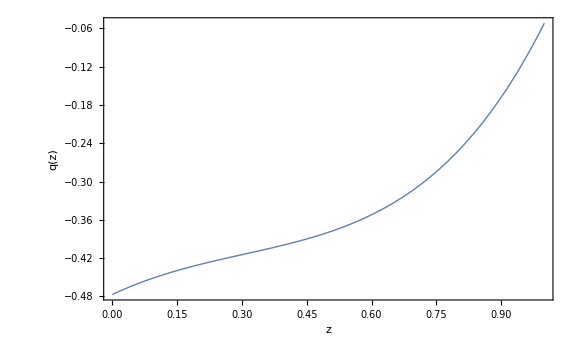

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.712983},{0.02,0.705953},{0.03,0.698913},{0.04,0.691866},{0.05,0.684813},{0.06,0.677758},{0.07,0.670703},{0.08,0.66365},{0.09,0.656601},{0.1,0.649559},{0.11,0.642525},{0.12,0.635501},{0.13,0.62849},{0.14,0.621493},{0.15,0.614512},{0.16,0.607549},{0.17,0.600605},{0.18,0.593682},{0.19,0.586782},{0.2,0.579906},{0.21,0.573054},{0.22,0.56623},{0.23,0.559433},{0.24,0.552666},{0.25,0.545929},{0.26,0.539224},{0.27,0.532551},{0.28,0.525912},{0.29,0.519308},{0.3,0.512739},{0.31,0.506207},{0.32,0.499712},{0.33,0.493256},{0.34,0.486838},{0.35,0.48046},{0.36,0.474123},{0.37,0.467827},{0.38,0.461572},{0.39,0.45536},{0.4,0.449191},{0.41,0.443066},{0.42,0.436984},{0.43,0.430947},{0.44,0.424955},{0.45,0.419008},{0.46,0.413108},{0.47,0.407253},{0.48,0.401445},{0.49,0.395684},{0.5,0.389969},{0.51,0.384303},{0.52,0.378684},{0.53,0.373113},{0.54,0.36759},{0.55,0.362115},{0.56,0.356689},{0.57,0.351312},{0.58,0.345984},{0.59,0.340704},{0.6,0.335474},{0.61,0.330293},{0.62,0.325161},{0.63,0.320078},{0.64,0.315045},{0.65,0.310061},{0.66,0.305126},{0.67,0.300241},{0.68,0.295405},{0.69,0.290619},{0.7,0.285882},{0.71,0.281194},{0.72,0.276556},{0.73,0.271967},{0.74,0.267427},{0.75,0.262936},{0.76,0.258493},{0.77,0.2541},{0.78,0.249756},{0.79,0.24546},{0.8,0.241212},{0.81,0.237013},{0.82,0.232862},{0.83,0.228759},{0.84,0.224704},{0.85,0.220696},{0.86,0.216737},{0.87,0.212824},{0.88,0.208959},{0.89,0.20514},{0.9,0.201368},{0.91,0.197643},{0.92,0.193964},{0.93,0.190331},{0.94,0.186744},{0.95,0.183203},{0.96,0.179707},{0.97,0.176256},{0.98,0.17285},{0.99,0.169489},{1.,0.166172}}

{{0.,0.28},{0.01,0.287017},{0.02,0.294047},{0.03,0.301087},{0.04,0.308134},{0.05,0.315187},{0.06,0.322242},{0.07,0.329297},{0.08,0.33635},{0.09,0.343399},{0.1,0.350441},{0.11,0.357475},{0.12,0.364499},{0.13,0.37151},{0.14,0.378507},{0.15,0.385488},{0.16,0.392451},{0.17,0.399395},{0.18,0.406318},{0.19,0.413218},{0.2,0.420094},{0.21,0.426946},{0.22,0.43377},{0.23,0.440567},{0.24,0.447334},{0.25,0.454071},{0.26,0.460776},{0.27,0.467449},{0.28,0.474088},{0.29,0.480692},{0.3,0.487261},{0.31,0.493793},{0.32,0.500288},{0.33,0.506744},{0.34,0.513162},{0.35,0.51954},{0.36,0.525877},{0.37,0.532173},{0.38,0.538428},{0.39,0.54464},{0.4,0.550809},{0.41,0.556934},{0.42,0.563016},{0.43,0.569053},{0.44,0.575045},{0.45,0.580992},{0.46,0.586892},{0.47,0.592747},{0.48,0.598555},{0.49,0.604316},{0.5,0.610031},{0.51,0.615697},{0.52,0.621316},{0.53,0.626887},{0.54,0.63241},{0.55,0.637885},{0.56,0.643311},{0.57,0.648688},{0.58,0.654016},{0.59,0.659296},{0.6,0.664526},{0.61,0.669707},{0.62,0.674839},{0.63,0.679922},{0.64,0.684955},{0.65,0.689939},{0.66,0.694874},{0.67,0.699759},{0.68,0.704595},{0.69,0.709381},{0.7,0.714118},{0.71,0.718806},{0.72,0.723444},{0.73,0.728033},{0.74,0.732573},{0.75,0.737064},{0.76,0.741507},{0.77,0.7459},{0.78,0.750244},{0.79,0.75454},{0.8,0.758788},{0.81,0.762987},{0.82,0.767138},{0.83,0.771241},{0.84,0.775296},{0.85,0.779304},{0.86,0.783263},{0.87,0.787176},{0.88,0.791041},{0.89,0.79486},{0.9,0.798632},{0.91,0.802357},{0.92,0.806036},{0.93,0.809669},{0.94,0.813256},{0.95,0.816797},{0.96,0.820293},{0.97,0.823744},{0.98,0.82715},{0.99,0.830511},{1.,0.833828}}

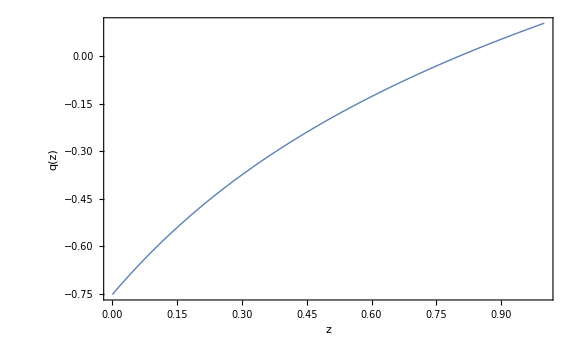

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.710164},{0.02,0.700386},{0.03,0.690676},{0.04,0.681041},{0.05,0.671491},{0.06,0.662033},{0.07,0.652673},{0.08,0.643418},{0.09,0.634272},{0.1,0.62524},{0.11,0.616326},{0.12,0.607534},{0.13,0.598866},{0.14,0.590326},{0.15,0.581914},{0.16,0.573634},{0.17,0.565485},{0.18,0.557469},{0.19,0.549587},{0.2,0.541838},{0.21,0.534223},{0.22,0.526741},{0.23,0.519392},{0.24,0.512176},{0.25,0.505091},{0.26,0.498136},{0.27,0.49131},{0.28,0.484612},{0.29,0.47804},{0.3,0.471594},{0.31,0.46527},{0.32,0.459068},{0.33,0.452986},{0.34,0.447022},{0.35,0.441175},{0.36,0.435441},{0.37,0.42982},{0.38,0.424309},{0.39,0.418907},{0.4,0.413611},{0.41,0.40842},{0.42,0.403331},{0.43,0.398343},{0.44,0.393454},{0.45,0.388661},{0.46,0.383962},{0.47,0.379357},{0.48,0.374842},{0.49,0.370417},{0.5,0.366078},{0.51,0.361825},{0.52,0.357656},{0.53,0.353568},{0.54,0.34956},{0.55,0.34563},{0.56,0.341777},{0.57,0.337998},{0.58,0.334293},{0.59,0.33066},{0.6,0.327096},{0.61,0.323601},{0.62,0.320173},{0.63,0.316811},{0.64,0.313512},{0.65,0.310276},{0.66,0.307102},{0.67,0.303987},{0.68,0.300931},{0.69,0.297932},{0.7,0.294989},{0.71,0.292101},{0.72,0.289266},{0.73,0.286483},{0.74,0.283752},{0.75,0.281071},{0.76,0.278439},{0.77,0.275854},{0.78,0.273317},{0.79,0.270825},{0.8,0.268378},{0.81,0.265974},{0.82,0.263614},{0.83,0.261295},{0.84,0.259017},{0.85,0.25678},{0.86,0.254581},{0.87,0.252421},{0.88,0.250299},{0.89,0.248213},{0.9,0.246163},{0.91,0.244149},{0.92,0.242169},{0.93,0.240222},{0.94,0.238309},{0.95,0.236427},{0.96,0.234578},{0.97,0.232759},{0.98,0.230971},{0.99,0.229212},{1.,0.227482}}

{{0.,0.28},{0.01,0.289836},{0.02,0.299614},{0.03,0.309324},{0.04,0.318959},{0.05,0.328509},{0.06,0.337967},{0.07,0.347327},{0.08,0.356582},{0.09,0.365728},{0.1,0.37476},{0.11,0.383674},{0.12,0.392466},{0.13,0.401134},{0.14,0.409674},{0.15,0.418086},{0.16,0.426366},{0.17,0.434515},{0.18,0.442531},{0.19,0.450413},{0.2,0.458162},{0.21,0.465777},{0.22,0.473259},{0.23,0.480608},{0.24,0.487824},{0.25,0.494909},{0.26,0.501864},{0.27,0.50869},{0.28,0.515388},{0.29,0.52196},{0.3,0.528406},{0.31,0.53473},{0.32,0.540932},{0.33,0.547014},{0.34,0.552978},{0.35,0.558825},{0.36,0.564559},{0.37,0.57018},{0.38,0.575691},{0.39,0.581093},{0.4,0.586389},{0.41,0.59158},{0.42,0.596669},{0.43,0.601657},{0.44,0.606546},{0.45,0.611339},{0.46,0.616038},{0.47,0.620643},{0.48,0.625158},{0.49,0.629583},{0.5,0.633922},{0.51,0.638175},{0.52,0.642344},{0.53,0.646432},{0.54,0.65044},{0.55,0.65437},{0.56,0.658223},{0.57,0.662002},{0.58,0.665707},{0.59,0.66934},{0.6,0.672904},{0.61,0.676399},{0.62,0.679827},{0.63,0.683189},{0.64,0.686488},{0.65,0.689724},{0.66,0.692898},{0.67,0.696013},{0.68,0.699069},{0.69,0.702068},{0.7,0.705011},{0.71,0.707899},{0.72,0.710734},{0.73,0.713517},{0.74,0.716248},{0.75,0.718929},{0.76,0.721561},{0.77,0.724146},{0.78,0.726683},{0.79,0.729175},{0.8,0.731622},{0.81,0.734026},{0.82,0.736386},{0.83,0.738705},{0.84,0.740983},{0.85,0.74322},{0.86,0.745419},{0.87,0.747579},{0.88,0.749701},{0.89,0.751787},{0.9,0.753837},{0.91,0.755851},{0.92,0.757831},{0.93,0.759778},{0.94,0.761691},{0.95,0.763573},{0.96,0.765422},{0.97,0.767241},{0.98,0.769029},{0.99,0.770788},{1.,0.772518}}

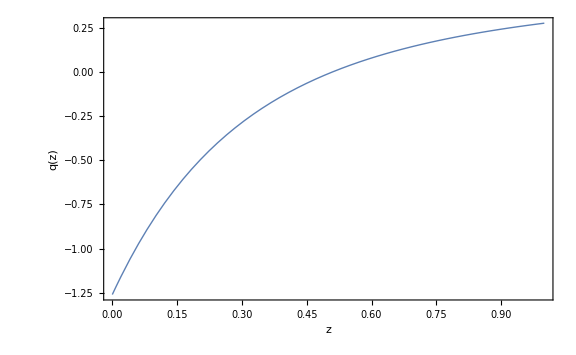

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,omegade[z]},{z,0,1,0.01}]
points8=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.72},{0.01,0.708761},{0.02,0.697629},{0.03,0.686618},{0.04,0.675739},{0.05,0.665004},{0.06,0.654423},{0.07,0.644002},{0.08,0.63375},{0.09,0.623672},{0.1,0.613772},{0.11,0.604055},{0.12,0.594522},{0.13,0.585176},{0.14,0.576018},{0.15,0.567049},{0.16,0.558269},{0.17,0.549677},{0.18,0.541272},{0.19,0.533053},{0.2,0.525018},{0.21,0.517165},{0.22,0.509492},{0.23,0.501996},{0.24,0.494674},{0.25,0.487524},{0.26,0.480543},{0.27,0.473727},{0.28,0.467073},{0.29,0.460578},{0.3,0.454239},{0.31,0.448051},{0.32,0.442013},{0.33,0.436119},{0.34,0.430368},{0.35,0.424755},{0.36,0.419277},{0.37,0.413931},{0.38,0.408714},{0.39,0.403622},{0.4,0.398652},{0.41,0.393801},{0.42,0.389066},{0.43,0.384444},{0.44,0.379932},{0.45,0.375527},{0.46,0.371226},{0.47,0.367026},{0.48,0.362925},{0.49,0.358921},{0.5,0.35501},{0.51,0.351189},{0.52,0.347458},{0.53,0.343812},{0.54,0.340251},{0.55,0.336771},{0.56,0.33337},{0.57,0.330047},{0.58,0.326799},{0.59,0.323624},{0.6,0.32052},{0.61,0.317486},{0.62,0.314519},{0.63,0.311617},{0.64,0.30878},{0.65,0.306005},{0.66,0.303291},{0.67,0.300635},{0.68,0.298037},{0.69,0.295495},{0.7,0.293008},{0.71,0.290573},{0.72,0.288191},{0.73,0.285858},{0.74,0.283575},{0.75,0.28134},{0.76,0.279151},{0.77,0.277008},{0.78,0.274909},{0.79,0.272853},{0.8,0.270839},{0.81,0.268866},{0.82,0.266933},{0.83,0.26504},{0.84,0.263184},{0.85,0.261365},{0.86,0.259583},{0.87,0.257836},{0.88,0.256123},{0.89,0.254444},{0.9,0.252798},{0.91,0.251184},{0.92,0.249602},{0.93,0.24805},{0.94,0.246527},{0.95,0.245034},{0.96,0.24357},{0.97,0.242133},{0.98,0.240723},{0.99,0.23934},{1.,0.237983}}

{{0.,0.28},{0.01,0.291239},{0.02,0.302371},{0.03,0.313382},{0.04,0.324261},{0.05,0.334996},{0.06,0.345577},{0.07,0.355998},{0.08,0.36625},{0.09,0.376328},{0.1,0.386228},{0.11,0.395945},{0.12,0.405478},{0.13,0.414824},{0.14,0.423982},{0.15,0.432951},{0.16,0.441731},{0.17,0.450323},{0.18,0.458728},{0.19,0.466947},{0.2,0.474982},{0.21,0.482835},{0.22,0.490508},{0.23,0.498004},{0.24,0.505326},{0.25,0.512476},{0.26,0.519457},{0.27,0.526273},{0.28,0.532927},{0.29,0.539422},{0.3,0.545761},{0.31,0.551949},{0.32,0.557987},{0.33,0.563881},{0.34,0.569632},{0.35,0.575245},{0.36,0.580723},{0.37,0.586069},{0.38,0.591286},{0.39,0.596378},{0.4,0.601348},{0.41,0.606199},{0.42,0.610934},{0.43,0.615556},{0.44,0.620068},{0.45,0.624473},{0.46,0.628774},{0.47,0.632974},{0.48,0.637075},{0.49,0.641079},{0.5,0.64499},{0.51,0.648811},{0.52,0.652542},{0.53,0.656188},{0.54,0.659749},{0.55,0.663229},{0.56,0.66663},{0.57,0.669953},{0.58,0.673201},{0.59,0.676376},{0.6,0.67948},{0.61,0.682514},{0.62,0.685481},{0.63,0.688383},{0.64,0.69122},{0.65,0.693995},{0.66,0.696709},{0.67,0.699365},{0.68,0.701963},{0.69,0.704505},{0.7,0.706992},{0.71,0.709427},{0.72,0.711809},{0.73,0.714142},{0.74,0.716425},{0.75,0.71866},{0.76,0.720849},{0.77,0.722992},{0.78,0.725091},{0.79,0.727147},{0.8,0.729161},{0.81,0.731134},{0.82,0.733067},{0.83,0.73496},{0.84,0.736816},{0.85,0.738635},{0.86,0.740417},{0.87,0.742164},{0.88,0.743877},{0.89,0.745556},{0.9,0.747202},{0.91,0.748816},{0.92,0.750398},{0.93,0.75195},{0.94,0.753473},{0.95,0.754966},{0.96,0.75643},{0.97,0.757867},{0.98,0.759277},{0.99,0.76066},{1.,0.762017}}

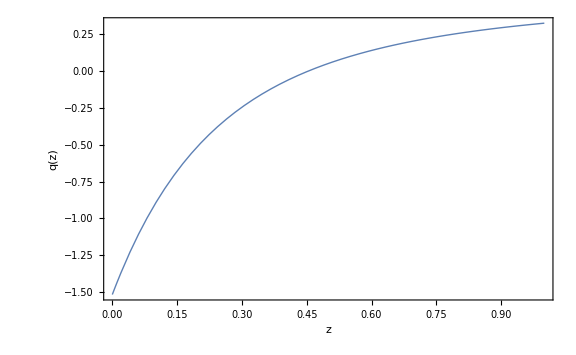

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

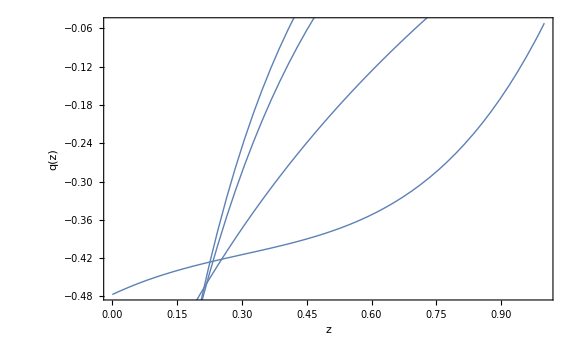

```mathematica
Show[p04n, p02n, p02, p04]
```

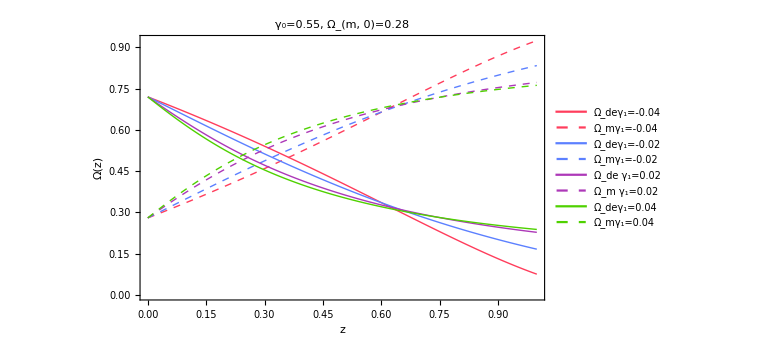

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7, points4, points8}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_1=-0.04","Ω_mγ_1=-0.04", "Ω_deγ_1=-0.02","Ω_mγ_1=-0.02", "Ω_de γ_1=0.02", "Ω_m γ_1=0.02","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.28", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
Export["omega(z)_gamma1_om0.28.pdf",list2,ImageResolution->500]
```

omega(z)_gamma1_om0.28.pdf

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.32;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.673961},{0.02,0.667898},{0.03,0.661813},{0.04,0.655704},{0.05,0.649573},{0.06,0.643421},{0.07,0.637246},{0.08,0.63105},{0.09,0.624833},{0.1,0.618596},{0.11,0.612338},{0.12,0.60606},{0.13,0.599762},{0.14,0.593445},{0.15,0.58711},{0.16,0.580755},{0.17,0.574383},{0.18,0.567992},{0.19,0.561584},{0.2,0.555159},{0.21,0.548717},{0.22,0.542259},{0.23,0.535785},{0.24,0.529296},{0.25,0.522791},{0.26,0.516272},{0.27,0.509739},{0.28,0.503192},{0.29,0.496632},{0.3,0.49006},{0.31,0.483475},{0.32,0.476879},{0.33,0.470272},{0.34,0.463655},{0.35,0.457028},{0.36,0.450392},{0.37,0.443747},{0.38,0.437095},{0.39,0.430436},{0.4,0.423771},{0.41,0.4171},{0.42,0.410425},{0.43,0.403746},{0.44,0.397064},{0.45,0.39038},{0.46,0.383695},{0.47,0.37701},{0.48,0.370326},{0.49,0.363643},{0.5,0.356964},{0.51,0.350288},{0.52,0.343618},{0.53,0.336954},{0.54,0.330297},{0.55,0.323649},{0.56,0.317012},{0.57,0.310385},{0.58,0.303771},{0.59,0.297172},{0.6,0.290588},{0.61,0.284021},{0.62,0.277472},{0.63,0.270943},{0.64,0.264437},{0.65,0.257953},{0.66,0.251494},{0.67,0.245062},{0.68,0.238659},{0.69,0.232286},{0.7,0.225945},{0.71,0.219638},{0.72,0.213367},{0.73,0.207135},{0.74,0.200942},{0.75,0.194791},{0.76,0.188684},{0.77,0.182624},{0.78,0.176613},{0.79,0.170652},{0.8,0.164745},{0.81,0.158893},{0.82,0.153099},{0.83,0.147365},{0.84,0.141694},{0.85,0.136088},{0.86,0.13055},{0.87,0.125082},{0.88,0.119688},{0.89,0.114369},{0.9,0.109129},{0.91,0.103969},{0.92,0.0988941},{0.93,0.0939056},{0.94,0.0890068},{0.95,0.0842006},{0.96,0.0794899},{0.97,0.0748776},{0.98,0.0703669},{0.99,0.0659607},{1.,0.0616623}}

{{0.,0.32},{0.01,0.326039},{0.02,0.332102},{0.03,0.338187},{0.04,0.344296},{0.05,0.350427},{0.06,0.356579},{0.07,0.362754},{0.08,0.36895},{0.09,0.375167},{0.1,0.381404},{0.11,0.387662},{0.12,0.39394},{0.13,0.400238},{0.14,0.406555},{0.15,0.41289},{0.16,0.419245},{0.17,0.425617},{0.18,0.432008},{0.19,0.438416},{0.2,0.444841},{0.21,0.451283},{0.22,0.457741},{0.23,0.464215},{0.24,0.470704},{0.25,0.477209},{0.26,0.483728},{0.27,0.490261},{0.28,0.496808},{0.29,0.503368},{0.3,0.50994},{0.31,0.516525},{0.32,0.523121},{0.33,0.529728},{0.34,0.536345},{0.35,0.542972},{0.36,0.549608},{0.37,0.556253},{0.38,0.562905},{0.39,0.569564},{0.4,0.576229},{0.41,0.5829},{0.42,0.589575},{0.43,0.596254},{0.44,0.602936},{0.45,0.60962},{0.46,0.616305},{0.47,0.62299},{0.48,0.629674},{0.49,0.636357},{0.5,0.643036},{0.51,0.649712},{0.52,0.656382},{0.53,0.663046},{0.54,0.669703},{0.55,0.676351},{0.56,0.682988},{0.57,0.689615},{0.58,0.696229},{0.59,0.702828},{0.6,0.709412},{0.61,0.715979},{0.62,0.722528},{0.63,0.729057},{0.64,0.735563},{0.65,0.742047},{0.66,0.748506},{0.67,0.754938},{0.68,0.761341},{0.69,0.767714},{0.7,0.774055},{0.71,0.780362},{0.72,0.786633},{0.73,0.792865},{0.74,0.799058},{0.75,0.805209},{0.76,0.811316},{0.77,0.817376},{0.78,0.823387},{0.79,0.829348},{0.8,0.835255},{0.81,0.841107},{0.82,0.846901},{0.83,0.852635},{0.84,0.858306},{0.85,0.863912},{0.86,0.86945},{0.87,0.874918},{0.88,0.880312},{0.89,0.885631},{0.9,0.890871},{0.91,0.896031},{0.92,0.901106},{0.93,0.906094},{0.94,0.910993},{0.95,0.915799},{0.96,0.92051},{0.97,0.925122},{0.98,0.929633},{0.99,0.934039},{1.,0.938338}}

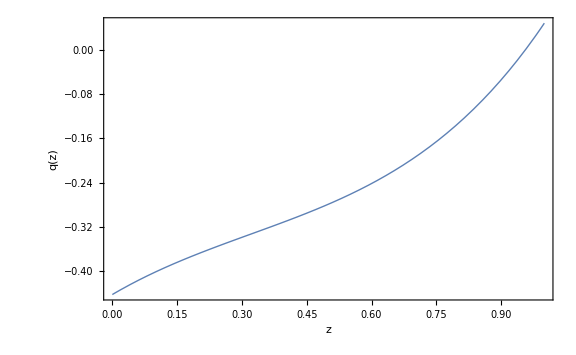

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.672751},{0.02,0.665509},{0.03,0.658276},{0.04,0.651053},{0.05,0.643844},{0.06,0.63665},{0.07,0.629474},{0.08,0.622317},{0.09,0.615181},{0.1,0.608068},{0.11,0.600979},{0.12,0.593917},{0.13,0.586882},{0.14,0.579877},{0.15,0.572903},{0.16,0.565961},{0.17,0.559051},{0.18,0.552177},{0.19,0.545338},{0.2,0.538536},{0.21,0.531772},{0.22,0.525046},{0.23,0.518361},{0.24,0.511716},{0.25,0.505112},{0.26,0.498551},{0.27,0.492033},{0.28,0.485559},{0.29,0.479129},{0.3,0.472744},{0.31,0.466405},{0.32,0.460112},{0.33,0.453865},{0.34,0.447666},{0.35,0.441514},{0.36,0.435411},{0.37,0.429356},{0.38,0.423349},{0.39,0.417392},{0.4,0.411484},{0.41,0.405626},{0.42,0.399818},{0.43,0.39406},{0.44,0.388352},{0.45,0.382695},{0.46,0.377088},{0.47,0.371532},{0.48,0.366027},{0.49,0.360573},{0.5,0.355171},{0.51,0.349819},{0.52,0.344519},{0.53,0.33927},{0.54,0.334072},{0.55,0.328925},{0.56,0.32383},{0.57,0.318786},{0.58,0.313793},{0.59,0.308851},{0.6,0.30396},{0.61,0.29912},{0.62,0.294331},{0.63,0.289592},{0.64,0.284904},{0.65,0.280267},{0.66,0.27568},{0.67,0.271143},{0.68,0.266657},{0.69,0.26222},{0.7,0.257833},{0.71,0.253495},{0.72,0.249207},{0.73,0.244968},{0.74,0.240778},{0.75,0.236637},{0.76,0.232544},{0.77,0.2285},{0.78,0.224503},{0.79,0.220555},{0.8,0.216654},{0.81,0.212801},{0.82,0.208995},{0.83,0.205235},{0.84,0.201522},{0.85,0.197856},{0.86,0.194236},{0.87,0.190661},{0.88,0.187133},{0.89,0.183649},{0.9,0.180211},{0.91,0.176817},{0.92,0.173468},{0.93,0.170162},{0.94,0.166901},{0.95,0.163683},{0.96,0.160509},{0.97,0.157377},{0.98,0.154289},{0.99,0.151242},{1.,0.148238}}

{{0.,0.32},{0.01,0.327249},{0.02,0.334491},{0.03,0.341724},{0.04,0.348947},{0.05,0.356156},{0.06,0.36335},{0.07,0.370526},{0.08,0.377683},{0.09,0.384819},{0.1,0.391932},{0.11,0.399021},{0.12,0.406083},{0.13,0.413118},{0.14,0.420123},{0.15,0.427097},{0.16,0.434039},{0.17,0.440949},{0.18,0.447823},{0.19,0.454662},{0.2,0.461464},{0.21,0.468228},{0.22,0.474954},{0.23,0.481639},{0.24,0.488284},{0.25,0.494888},{0.26,0.501449},{0.27,0.507967},{0.28,0.514441},{0.29,0.520871},{0.3,0.527256},{0.31,0.533595},{0.32,0.539888},{0.33,0.546135},{0.34,0.552334},{0.35,0.558486},{0.36,0.564589},{0.37,0.570644},{0.38,0.576651},{0.39,0.582608},{0.4,0.588516},{0.41,0.594374},{0.42,0.600182},{0.43,0.60594},{0.44,0.611648},{0.45,0.617305},{0.46,0.622912},{0.47,0.628468},{0.48,0.633973},{0.49,0.639427},{0.5,0.644829},{0.51,0.650181},{0.52,0.655481},{0.53,0.66073},{0.54,0.665928},{0.55,0.671075},{0.56,0.67617},{0.57,0.681214},{0.58,0.686207},{0.59,0.691149},{0.6,0.69604},{0.61,0.70088},{0.62,0.705669},{0.63,0.710408},{0.64,0.715096},{0.65,0.719733},{0.66,0.72432},{0.67,0.728857},{0.68,0.733343},{0.69,0.73778},{0.7,0.742167},{0.71,0.746505},{0.72,0.750793},{0.73,0.755032},{0.74,0.759222},{0.75,0.763363},{0.76,0.767456},{0.77,0.7715},{0.78,0.775497},{0.79,0.779445},{0.8,0.783346},{0.81,0.787199},{0.82,0.791005},{0.83,0.794765},{0.84,0.798478},{0.85,0.802144},{0.86,0.805764},{0.87,0.809339},{0.88,0.812867},{0.89,0.816351},{0.9,0.819789},{0.91,0.823183},{0.92,0.826532},{0.93,0.829838},{0.94,0.833099},{0.95,0.836317},{0.96,0.839491},{0.97,0.842623},{0.98,0.845711},{0.99,0.848758},{1.,0.851762}}

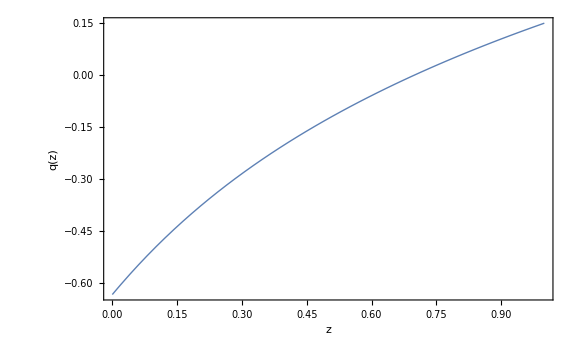

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.669879},{0.02,0.659857},{0.03,0.649943},{0.04,0.640142},{0.05,0.630462},{0.06,0.620908},{0.07,0.611484},{0.08,0.602195},{0.09,0.593045},{0.1,0.584035},{0.11,0.575168},{0.12,0.566447},{0.13,0.557872},{0.14,0.549444},{0.15,0.541164},{0.16,0.533033},{0.17,0.525049},{0.18,0.517213},{0.19,0.509525},{0.2,0.501982},{0.21,0.494584},{0.22,0.48733},{0.23,0.480217},{0.24,0.473246},{0.25,0.466414},{0.26,0.459718},{0.27,0.453157},{0.28,0.44673},{0.29,0.440433},{0.3,0.434265},{0.31,0.428224},{0.32,0.422307},{0.33,0.416513},{0.34,0.410838},{0.35,0.40528},{0.36,0.399838},{0.37,0.394509},{0.38,0.389291},{0.39,0.384181},{0.4,0.379176},{0.41,0.374276},{0.42,0.369478},{0.43,0.364779},{0.44,0.360177},{0.45,0.35567},{0.46,0.351257},{0.47,0.346934},{0.48,0.3427},{0.49,0.338554},{0.5,0.334492},{0.51,0.330513},{0.52,0.326615},{0.53,0.322796},{0.54,0.319054},{0.55,0.315388},{0.56,0.311796},{0.57,0.308276},{0.58,0.304827},{0.59,0.301446},{0.6,0.298133},{0.61,0.294885},{0.62,0.291701},{0.63,0.288579},{0.64,0.285519},{0.65,0.282519},{0.66,0.279576},{0.67,0.276691},{0.68,0.273862},{0.69,0.271086},{0.7,0.268364},{0.71,0.265694},{0.72,0.263074},{0.73,0.260504},{0.74,0.257982},{0.75,0.255507},{0.76,0.253079},{0.77,0.250695},{0.78,0.248356},{0.79,0.246059},{0.8,0.243805},{0.81,0.241592},{0.82,0.239419},{0.83,0.237285},{0.84,0.23519},{0.85,0.233132},{0.86,0.231111},{0.87,0.229126},{0.88,0.227176},{0.89,0.225261},{0.9,0.223379},{0.91,0.221529},{0.92,0.219712},{0.93,0.217927},{0.94,0.216172},{0.95,0.214447},{0.96,0.212751},{0.97,0.211084},{0.98,0.209446},{0.99,0.207835},{1.,0.206251}}

{{0.,0.32},{0.01,0.330121},{0.02,0.340143},{0.03,0.350057},{0.04,0.359858},{0.05,0.369538},{0.06,0.379092},{0.07,0.388516},{0.08,0.397805},{0.09,0.406955},{0.1,0.415965},{0.11,0.424832},{0.12,0.433553},{0.13,0.442128},{0.14,0.450556},{0.15,0.458836},{0.16,0.466967},{0.17,0.474951},{0.18,0.482787},{0.19,0.490475},{0.2,0.498018},{0.21,0.505416},{0.22,0.51267},{0.23,0.519783},{0.24,0.526754},{0.25,0.533586},{0.26,0.540282},{0.27,0.546843},{0.28,0.55327},{0.29,0.559567},{0.3,0.565735},{0.31,0.571776},{0.32,0.577693},{0.33,0.583487},{0.34,0.589162},{0.35,0.59472},{0.36,0.600162},{0.37,0.605491},{0.38,0.610709},{0.39,0.615819},{0.4,0.620824},{0.41,0.625724},{0.42,0.630522},{0.43,0.635221},{0.44,0.639823},{0.45,0.64433},{0.46,0.648743},{0.47,0.653066},{0.48,0.6573},{0.49,0.661446},{0.5,0.665508},{0.51,0.669487},{0.52,0.673385},{0.53,0.677204},{0.54,0.680946},{0.55,0.684612},{0.56,0.688204},{0.57,0.691724},{0.58,0.695173},{0.59,0.698554},{0.6,0.701867},{0.61,0.705115},{0.62,0.708299},{0.63,0.711421},{0.64,0.714481},{0.65,0.717481},{0.66,0.720424},{0.67,0.723309},{0.68,0.726138},{0.69,0.728914},{0.7,0.731636},{0.71,0.734306},{0.72,0.736926},{0.73,0.739496},{0.74,0.742018},{0.75,0.744493},{0.76,0.746921},{0.77,0.749305},{0.78,0.751644},{0.79,0.753941},{0.8,0.756195},{0.81,0.758408},{0.82,0.760581},{0.83,0.762715},{0.84,0.76481},{0.85,0.766868},{0.86,0.768889},{0.87,0.770874},{0.88,0.772824},{0.89,0.774739},{0.9,0.776621},{0.91,0.778471},{0.92,0.780288},{0.93,0.782073},{0.94,0.783828},{0.95,0.785553},{0.96,0.787249},{0.97,0.788916},{0.98,0.790554},{0.99,0.792165},{1.,0.793749}}

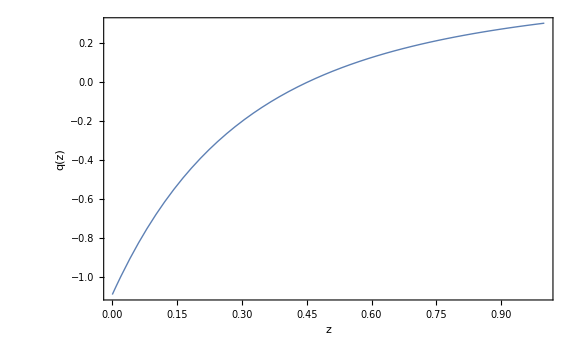

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,omegade[z]},{z,0,1,0.01}]
points8=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.68},{0.01,0.66845},{0.02,0.657062},{0.03,0.645846},{0.04,0.634811},{0.05,0.623966},{0.06,0.613316},{0.07,0.602866},{0.08,0.592621},{0.09,0.582584},{0.1,0.572755},{0.11,0.563137},{0.12,0.553729},{0.13,0.544532},{0.14,0.535544},{0.15,0.526764},{0.16,0.51819},{0.17,0.509819},{0.18,0.50165},{0.19,0.493678},{0.2,0.485902},{0.21,0.478317},{0.22,0.47092},{0.23,0.463707},{0.24,0.456675},{0.25,0.449819},{0.26,0.443136},{0.27,0.436621},{0.28,0.430271},{0.29,0.424082},{0.3,0.418049},{0.31,0.41217},{0.32,0.406439},{0.33,0.400853},{0.34,0.395408},{0.35,0.390101},{0.36,0.384927},{0.37,0.379883},{0.38,0.374966},{0.39,0.370172},{0.4,0.365498},{0.41,0.360939},{0.42,0.356494},{0.43,0.352159},{0.44,0.34793},{0.45,0.343806},{0.46,0.339782},{0.47,0.335856},{0.48,0.332025},{0.49,0.328286},{0.5,0.324638},{0.51,0.321077},{0.52,0.317601},{0.53,0.314207},{0.54,0.310893},{0.55,0.307658},{0.56,0.304498},{0.57,0.301411},{0.58,0.298397},{0.59,0.295451},{0.6,0.292573},{0.61,0.289762},{0.62,0.287014},{0.63,0.284328},{0.64,0.281702},{0.65,0.279136},{0.66,0.276626},{0.67,0.274172},{0.68,0.271773},{0.69,0.269426},{0.7,0.26713},{0.71,0.264884},{0.72,0.262687},{0.73,0.260537},{0.74,0.258433},{0.75,0.256373},{0.76,0.254358},{0.77,0.252385},{0.78,0.250453},{0.79,0.248562},{0.8,0.24671},{0.81,0.244897},{0.82,0.24312},{0.83,0.241381},{0.84,0.239676},{0.85,0.238006},{0.86,0.23637},{0.87,0.234767},{0.88,0.233196},{0.89,0.231656},{0.9,0.230147},{0.91,0.228667},{0.92,0.227217},{0.93,0.225795},{0.94,0.2244},{0.95,0.223033},{0.96,0.221692},{0.97,0.220377},{0.98,0.219087},{0.99,0.217821},{1.,0.21658}}

{{0.,0.32},{0.01,0.33155},{0.02,0.342938},{0.03,0.354154},{0.04,0.365189},{0.05,0.376034},{0.06,0.386684},{0.07,0.397134},{0.08,0.407379},{0.09,0.417416},{0.1,0.427245},{0.11,0.436863},{0.12,0.446271},{0.13,0.455468},{0.14,0.464456},{0.15,0.473236},{0.16,0.48181},{0.17,0.490181},{0.18,0.49835},{0.19,0.506322},{0.2,0.514098},{0.21,0.521683},{0.22,0.52908},{0.23,0.536293},{0.24,0.543325},{0.25,0.550181},{0.26,0.556864},{0.27,0.563379},{0.28,0.569729},{0.29,0.575918},{0.3,0.581951},{0.31,0.58783},{0.32,0.593561},{0.33,0.599147},{0.34,0.604592},{0.35,0.609899},{0.36,0.615073},{0.37,0.620117},{0.38,0.625034},{0.39,0.629828},{0.4,0.634502},{0.41,0.639061},{0.42,0.643506},{0.43,0.647841},{0.44,0.65207},{0.45,0.656194},{0.46,0.660218},{0.47,0.664144},{0.48,0.667975},{0.49,0.671714},{0.5,0.675362},{0.51,0.678923},{0.52,0.682399},{0.53,0.685793},{0.54,0.689107},{0.55,0.692342},{0.56,0.695502},{0.57,0.698589},{0.58,0.701603},{0.59,0.704549},{0.6,0.707427},{0.61,0.710238},{0.62,0.712986},{0.63,0.715672},{0.64,0.718298},{0.65,0.720864},{0.66,0.723374},{0.67,0.725828},{0.68,0.728227},{0.69,0.730574},{0.7,0.73287},{0.71,0.735116},{0.72,0.737313},{0.73,0.739463},{0.74,0.741567},{0.75,0.743627},{0.76,0.745642},{0.77,0.747615},{0.78,0.749547},{0.79,0.751438},{0.8,0.75329},{0.81,0.755103},{0.82,0.75688},{0.83,0.758619},{0.84,0.760324},{0.85,0.761994},{0.86,0.76363},{0.87,0.765233},{0.88,0.766804},{0.89,0.768344},{0.9,0.769853},{0.91,0.771333},{0.92,0.772783},{0.93,0.774205},{0.94,0.7756},{0.95,0.776967},{0.96,0.778308},{0.97,0.779623},{0.98,0.780913},{0.99,0.782179},{1.,0.78342}}

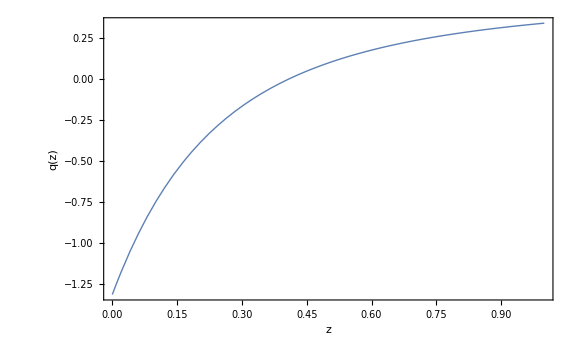

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

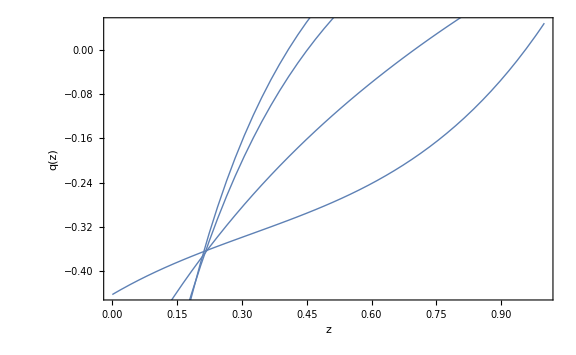

```mathematica
Show[p04n, p02n, p02, p04]
```

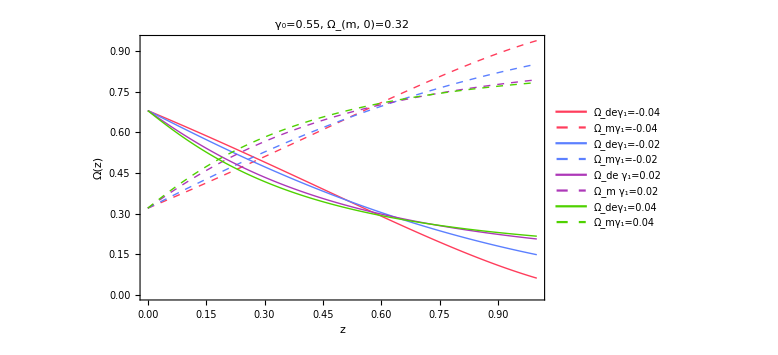

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7, points4, points8}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_1=-0.04","Ω_mγ_1=-0.04", "Ω_deγ_1=-0.02","Ω_mγ_1=-0.02", "Ω_de γ_1=0.02", "Ω_m γ_1=0.02","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.32", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
Export["omega(z)_gamma1_om0.32.pdf",list2,ImageResolution->500]
```